```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
eqs=<<eqs.m;
bcsr1=<<bcsr1.m;
bcsr0=<<bcsr0.m;
jacobi=<<jacobi.m;
jacobir1=<<jacobir1.m;
jacobir0=<<jacobir0.m;
check=<<check.m;
```

## Preparation

```mathematica
(*Parameters*)
L=1;Lr=1.0;Lx=30.0;mu=5.6;
e=0.25;tc=0.2099;tau=0.5;t=tau tc;T=t mu;
zh=1/6 (4 π T+√(16 π^2 T^2+3e mu^2));
Nr=30;Nx=150;Nrx=Nr*Nx;
Eye=IdentityMatrix[Nrx];Zero=ConstantArray[0,{Nrx,Nrx}];
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
dr=cheb[Nr,Lr];
drs[0]=IdentityMatrix[Nr];drs[1]=dr;drs[2]=dr.dr;
gridr=0.5(chebp[Nr]+1);rr=gridr⊗ConstantArray[1,Nx];R=Flatten[rr];
(*boundary index of holographic coordinate*)
r1=Flatten[Position[R,n_/;n==gridr⟦1⟧]];r0=Flatten[Position[R,n_/;n==gridr⟦-1⟧]];
rb=Join[r0,r1];
(*Fourier谱求导矩阵生成函数*)
fourier[n_,l_]:=π/l Table[If[i==j,0,(-1)^(i-j)If[Mod[n,2]==0,Cot[(π*(i-j))/n],Csc[(π*(i-j))/n]]],{i,1,n},{j,1,n}];
dx=fourier[Nx,Lx];
dxs[0]=IdentityMatrix[Nx];dxs[1]=dx;dxs[2]=dx.dx;
gridx=Lx/Nx Range[-Nx/2,Nx/2-1];xx=ConstantArray[1,Nr]⊗gridx;X=Flatten[xx];
(*derivative matrix after vectorization*)
Do[If[i+j≤ 2,ds[i,j]=KroneckerProduct[drs[i],dxs[j]]],{i,0,2},{j,0,2}];
```

## Solution

### initialization

```mathematica
SetDirectory["data"];
last=1;
If[last==1,
(*last outcome*)
q[1]=S[Q1]=<<Q1.m;
q[2]=S[Q2]=<<Q2.m;
q[3]=S[Q3]=<<Q3.m;
q[4]=S[Q4]=<<Q4.m;
q[5]=S[Q5]=<<Q5.m;
q[6]=S[Q6]=<<Q6.m;
q[7]=S[Q7]=<<Q7.m;,
(*seed*)
q[1]=S[Q1]=ConstantArray[1,Nrx];
q[2]=S[Q2]=ConstantArray[1,Nrx];
q[3]=S[Q3]=ConstantArray[0,Nrx];
q[4]=S[Q4]=ConstantArray[1,Nrx];
q[5]=S[Q5]=ConstantArray[1,Nrx];
q[6]=S[Q6]=4 Tanh[X-Lx/4]Tanh[-X-Lx/4];
q[7]=S[Q7]=ConstantArray[0.5,Nrx];]
(*j=3;
q[1]=S[Q1]=ReadList["Q1.m"]⟦j⟧;
q[2]=S[Q2]=ReadList["Q2.m"]⟦j⟧;
q[3]=S[Q3]=ReadList["Q3.m"]⟦j⟧;
q[4]=S[Q4]=ReadList["Q4.m"]⟦j⟧;
q[5]=S[Q5]=ReadList["Q5.m"]⟦j⟧;
q[6]=S[Q6]=ReadList["Q6.m"]⟦j⟧;
q[7]=S[Q7]=ReadList["Q7.m"]⟦j⟧;*)
(*reshape*)
Do[req[i]=ArrayReshape[q[i],{Nr,Nx}],{i,7}];
(*interpolate function*)
Do[interfunq[i]=ListInterpolation[Append[req[i]ᵀ,req[i]⟦;;,1⟧]ᵀ,{gridr,Append[gridx,0.5Lx]}],{i,7}];
```

### interpolation

```mathematica
(*resample*)
Do[q[k]=Flatten[Table[interfunq[k][gridr⟦i⟧,gridx⟦j⟧],{i,Nr},{j,Nx}]],{k,7}];
{S[Q1],S[Q2],S[Q3],S[Q4],S[Q5],S[Q6],S[Q7]}={q[1],q[2],q[3],q[4],q[5],q[6],q[7]};
```

### iteration

```mathematica
seed=Join[q[1],q[2],q[3],q[4],q[5],q[6],q[7]];length=Length[seed];
eps=10^-10;k=0;kmax=9;done=1;rmssollist={};
Monitor[While[done==1&&k<kmax,
diseqs=eqs/.{Derivative[i_,j_][h_][r,x]->ds[i,j].S[h],h_[r,x]->S[h],r->R};
disbcsr1=bcsr1/.{Derivative[i_,j_][h_][r,x]:>(ds[i,j]⟦r1⟧).S[h],h_[r,x]:>S[h]⟦r1⟧};
disbcsr0=bcsr0/.{Derivative[i_,j_][h_][r,x]:>(ds[i,j]⟦r0⟧).S[h],h_[r,x]:>S[h]⟦r0⟧};
diseqs⟦;;,r1⟧=disbcsr1;
diseqs⟦;;,r0⟧=disbcsr0;
b=-Flatten[diseqs];
	
J=jacobi/.{Derivative[i_,j_][h_][r,x]->ds[i,j].S[h],h_[r,x]->S[h],Subscript[d, i_,j_]->ds[i,j],eye->Eye,zero->Zero,r->R};
Jr1=jacobir1/.{Derivative[i_,j_][h_][r,x]:> (ds[i,j]⟦r1⟧).S[h],h_[r,x]:> S[h]⟦r1⟧,Subscript[d, i_,j_]:> ds[i,j]⟦r1⟧,eye:> Eye⟦r1⟧,zero:> Zero⟦r1⟧};
Jr0=jacobir0/.{Derivative[i_,j_][h_][r,x]:> (ds[i,j]⟦r0⟧).S[h],h_[r,x]:> S[h]⟦r0⟧,Subscript[d, i_,j_]:> ds[i,j]⟦r0⟧,eye:> Eye⟦r0⟧,zero:> Zero⟦r0⟧};
J⟦;;,;;,r1⟧=Jr1;
J⟦;;,;;,r0⟧=Jr0;
J=ArrayFlatten[J];
sol=LinearSolve[J,b];
seed+=sol;k++;
reseed=ArrayReshape[seed,{7,Nrx}];
q[1]=S[Q1]=reseed⟦1⟧;
q[2]=S[Q2]=reseed⟦2⟧;
q[3]=S[Q3]=reseed⟦3⟧;
q[4]=S[Q4]=reseed⟦4⟧;
q[5]=S[Q5]=reseed⟦5⟧;
q[6]=S[Q6]=reseed⟦6⟧;
q[7]=S[Q7]=reseed⟦7⟧;
rmssol=√(Total[sol^2]/length);
AppendTo[rmssollist,rmssol];
If[rmssol≤eps,done=0];
],rmssollist]
Print[rmssollist];
```

LinearSolve::luc: 病态矩阵 {«1»} 构成的 LinearSolve 的结果可能包含明显的数值错误.

General::stop: 在本次计算中，LinearSolve::luc 的进一步输出将被抑制.

{0.396734,0.124069,0.0268552,0.000701712,4.71007×10^-7,1.00136×10^-8,5.87209×10^-9,5.33352×10^-9,1.7975×10^-8}

### data and visualization

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

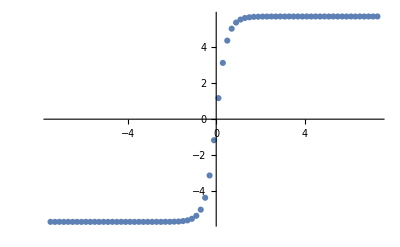

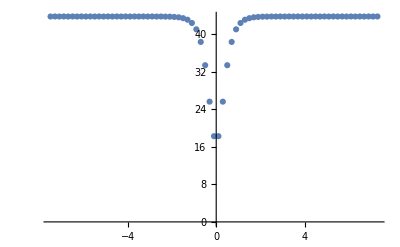

{a→5.69547,ξ→0.494873}

{a→26.3736,ξ→-0.484264,c→43.7384}

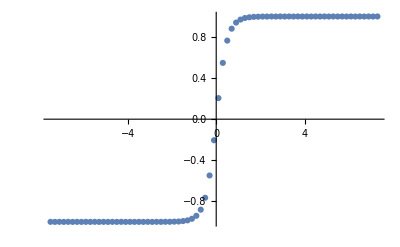

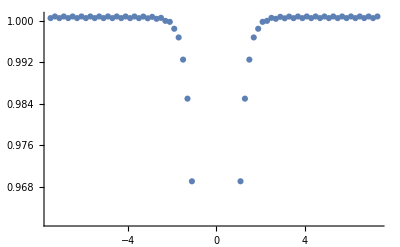

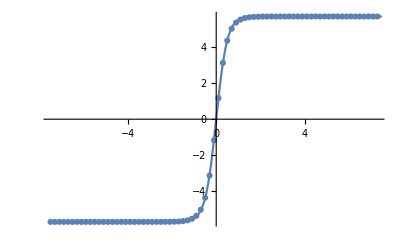

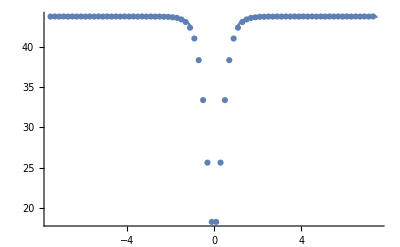

```mathematica
Gridr=Reverse[gridr];
Gridx=gridx+Lx/4;
Do[solq[i]=ArrayReshape[q[i],{Nr,Nx}],{i,7}];
orderp=(solq[6]⟦1⟧);
density=mu zh(1-1/2(-dr⟦1⟧.solq[7]));
ListPlot3D[Flatten[Table[{Gridr⟦i⟧,Gridx⟦j⟧,solq[6]⟦i,j⟧},{i,Nr},{j,Nx/2}],1],PlotRange->All,LabelStyle->Directive[Black, FontFamily->"Times New Roman",Black,12],AxesLabel->{Style["r",Italic,14],Style["x",Italic,14],Style["Q_6",14]}]
ListPlot3D[Flatten[Table[{Gridr⟦i⟧,Gridx⟦j⟧,solq[7]⟦i,j⟧},{i,Nr},{j,Nx/2}],1],PlotRange->All,LabelStyle->Directive[Black, FontFamily->"Times New Roman",Black,12],AxesLabel->{Style["r",Italic,14],Style["x",Italic,14],Style["Q_7",14]}]
ListPlot3D[Flatten[Table[{Gridr⟦i⟧,Gridx⟦j⟧,solq[1]⟦i,j⟧},{i,Nr},{j,Nx/2}],1],PlotRange->All,LabelStyle->Directive[Black, FontFamily->"Times New Roman",Black,12],AxesLabel->{Style["r",Italic,14],Style["x",Italic,14],Style["Q_1",14]}]
ListPlot3D[Flatten[Table[{Gridr⟦i⟧,Gridx⟦j⟧,solq[2]⟦i,j⟧},{i,Nr},{j,Nx/2}],1],PlotRange->All,LabelStyle->Directive[Black, FontFamily->"Times New Roman",Black,12],AxesLabel->{Style["r",Italic,14],Style["x",Italic,14],Style["Q_2",14]}]
ListPlot3D[Flatten[Table[{Gridr⟦i⟧,Gridx⟦j⟧,solq[3]⟦i,j⟧},{i,Nr},{j,Nx/2}],1],PlotRange->All,LabelStyle->Directive[Black, FontFamily->"Times New Roman",Black,12],AxesLabel->{Style["r",Italic,14],Style["x",Italic,14],Style["Q_3",14]}]
ListPlot3D[Flatten[Table[{Gridr⟦i⟧,Gridx⟦j⟧,solq[4]⟦i,j⟧},{i,Nr},{j,Nx/2}],1],PlotRange->All,LabelStyle->Directive[Black, FontFamily->"Times New Roman",Black,12],AxesLabel->{Style["r",Italic,14],Style["x",Italic,14],Style["Q_4",14]}]
ListPlot3D[Flatten[Table[{Gridr⟦i⟧,Gridx⟦j⟧,solq[5]⟦i,j⟧},{i,Nr},{j,Nx/2}],1],PlotRange->All,LabelStyle->Directive[Black, FontFamily->"Times New Roman",Black,12],AxesLabel->{Style["r",Italic,14],Style["x",Italic,14],Style["Q_5",14]}]
ListPlot[Table[{Gridx⟦i⟧,orderp⟦i⟧},{i,1,Nx/2}],PlotRange->All]
ListPlot[Table[{Gridx⟦i⟧,density⟦i⟧},{i,1,Nx/2}],PlotRange->All]
fitorderp=FindFit[Table[{Gridx⟦i⟧,orderp⟦i⟧},{i,Nx/2}],a Tanh[x/ξ],{a,ξ},x]
fitdensity=FindFit[Table[{Gridx⟦i⟧,density⟦i⟧},{i,Nx/2}],-a Sech[x/ξ]^2+c,{a,ξ,c},x]
ListPlot[Table[{Gridx⟦i⟧,1/a orderp⟦i⟧/.fitorderp},{i,Nx/2}]]
ListPlot[Table[{Gridx⟦i⟧,1/c density⟦i⟧/.fitdensity},{i,Nx/2}]]
Show[ListPlot[Table[{Gridx⟦i⟧,orderp⟦i⟧},{i,Nx/2}]],Plot[a Tanh[x/ξ]/.fitorderp,{x,-Lx/4,Lx/4}]]
Show[ListPlot[Table[{Gridx⟦i⟧,density⟦i⟧},{i,Nx/2}],PlotRange->All],Plot[(-a Sech[x/ξ]^2+c)/.fitdensity,{x,-Lx/4,Lx/4}],PlotRange->All]
```

### double soliton fit

{a→5.69544,ξ→0.494885}

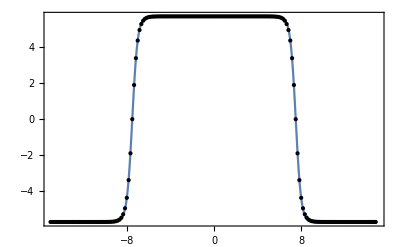

{a→26.3748,ξ→-0.484238,c→43.7382}

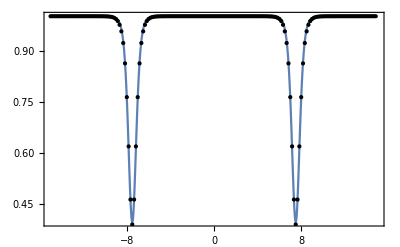

```mathematica
fitorderp=FindFit[Table[{gridx⟦i⟧,orderp⟦i⟧},{i,Nx}],a Tanh[(x-Lx/4)/ξ]Tanh[(-x-Lx/4)/ξ],{a,ξ},x]
Plot[a Tanh[(x-Lx/4)/ξ]Tanh[(-x-Lx/4)/ξ]/.fitorderp,{x,-Lx/2,Lx/2},PlotRange->All,Epilog->Point[Table[{gridx⟦i⟧,orderp⟦i⟧},{i,Nx}]],Frame->True]
fitdensity=FindFit[Table[{gridx⟦i⟧,density⟦i⟧},{i,Nx}],-a (Sech[(x+Lx/4)/ξ]^2+Sech[(x-Lx/4)/ξ]^2)+c,{a,ξ,c},x]
Plot[1/c(-a (Sech[(x+Lx/4)/ξ]^2+Sech[(x-Lx/4)/ξ]^2)+c)/.fitdensity,{x,-Lx/2,Lx/2},PlotRange->All,Epilog->Point[Table[{gridx⟦i⟧,1/c density⟦i⟧/.fitdensity},{i,Nx}]],Frame->True]
```

### check DeTurck vector

```mathematica
submonitor=check/.{Derivative[i_,j_][h_][r,x]->ds[i,j].S[h],h_[r,x]->S[h],r->R};
submonitor⟦rb⟧=0;
rmsxi=√(Total[submonitor^2]/Length[submonitor])
```

Power::infy: 碰到无穷表达式 1/0.^2.

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

4.15246×10^-9

## Thermodynamics

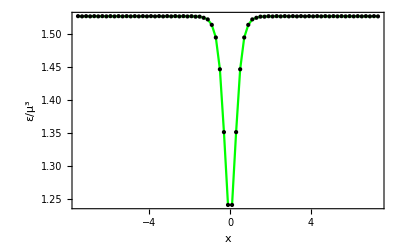

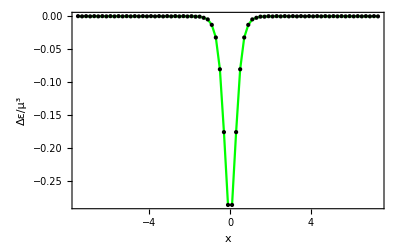

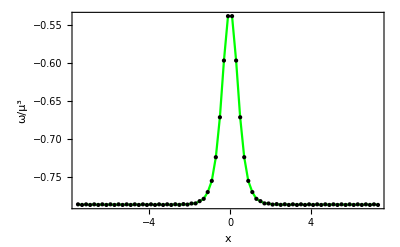

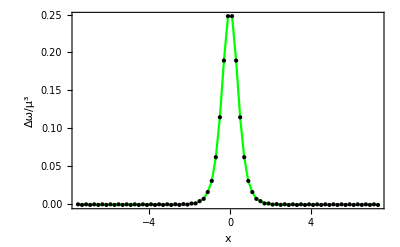

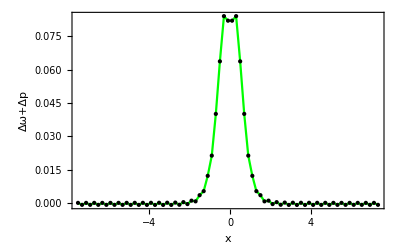

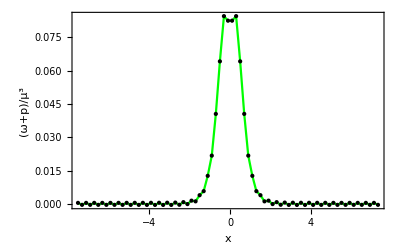

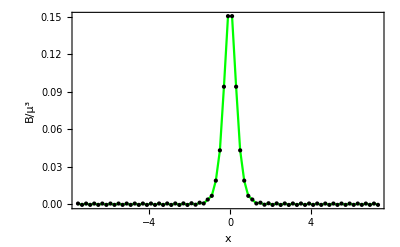

```mathematica
dr3=dr.dr.dr;
ε= zh/e ((e mu^2)/2+2 zh^2+zh^2/16(dr3⟦1⟧.solq[1])+3/8 e (solq[6]⟦1⟧)^2);
s=(4π zh^2)/e √(solq[4]⟦-1⟧solq[5]⟦-1⟧);
n=density;
ω=ε-T s-mu n;
p=zh/e((e mu^2)/4+zh^2-zh^2/32 ((dr3⟦1⟧.solq[4])+(dr3⟦1⟧.solq[5]))-3/8 e (solq[6]⟦1⟧)^2);
B=zh^3/(32e)(-(dr3⟦1⟧.solq[4])+(dr3⟦1⟧.solq[5]));
ListLinePlot[Table[{Gridx⟦i⟧,(1/mu^3)ε⟦i⟧},{i,1,Nx/2}],Frame->True,PlotRange->All,PlotStyle->Green,LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],FrameLabel->{Style["x",14,Italic],Style["ε/μ^3",14]},RotateLabel->False,Epilog->Point[Table[{Gridx⟦i⟧,(1/mu^3)ε⟦i⟧},{i,1,Nx/2}]]]
ListLinePlot[Table[{Gridx⟦i⟧,(1/mu^3)(ε⟦i⟧-ε⟦1⟧)},{i,1,Nx/2}],Frame->True,PlotRange->All,PlotStyle->Green,LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],FrameLabel->{Style["x",14,Italic],Style["Δε/μ^3",14]},RotateLabel->False,Epilog->Point[Table[{Gridx⟦i⟧,(1/mu^3)(ε⟦i⟧-ε⟦1⟧)},{i,1,Nx/2}]]]
ListLinePlot[Table[{Gridx⟦i⟧,(1/mu^3)ω⟦i⟧},{i,1,Nx/2}],Frame->True,PlotRange->All,PlotStyle->Green,LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],FrameLabel->{Style["x",14,Italic],Style["ω/μ^3",14]},RotateLabel->False,Epilog->Point[Table[{Gridx⟦i⟧,(1/mu^3)ω⟦i⟧},{i,1,Nx/2}]]]
ListLinePlot[Table[{Gridx⟦i⟧,(1/mu^3)(ω⟦i⟧-ω⟦1⟧)},{i,1,Nx/2}],Frame->True,PlotRange->All,PlotStyle->Green,LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],FrameLabel->{Style["x",14,Italic],Style["Δω/μ^3",14]},RotateLabel->False,Epilog->Point[Table[{Gridx⟦i⟧,(1/mu^3)(ω⟦i⟧-ω⟦1⟧)},{i,1,Nx/2}]]]
ListLinePlot[Table[{Gridx⟦i⟧,(1/mu^3)((ω⟦i⟧-ω⟦1⟧)+(p⟦i⟧-p⟦1⟧))},{i,1,Nx/2}],Frame->True,PlotRange->All,PlotStyle->Green,LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],FrameLabel->{Style["x",14,Italic],Style["Δω+Δp",14]},RotateLabel->False,Epilog->Point[Table[{Gridx⟦i⟧,(1/mu^3)((ω⟦i⟧-ω⟦1⟧)+(p⟦i⟧-p⟦1⟧))},{i,1,Nx/2}]]]
ListLinePlot[Table[{Gridx⟦i⟧,(1/mu^3)(ω⟦i⟧+p⟦i⟧)},{i,1,Nx/2}],Frame->True,PlotRange->All,PlotStyle->Green,LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],FrameLabel->{Style["x",14,Italic],Style["(ω+p)/μ^3",14]},RotateLabel->False,Epilog->Point[Table[{Gridx⟦i⟧,(1/mu^3)(ω⟦i⟧+p⟦i⟧)},{i,1,Nx/2}]]]
ListLinePlot[Table[{Gridx⟦i⟧,(1/mu^3)B⟦i⟧},{i,1,Nx/2}],Frame->True,PlotRange->All,PlotStyle->Green,LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],FrameLabel->{Style["x",14,Italic],Style["B/μ^3",14]},RotateLabel->False,Epilog->Point[Table[{Gridx⟦i⟧,(1/mu^3)B⟦i⟧},{i,1,Nx/2}]]]
```

## data export

### changes of healing length and depletion with back-reaction at fixed temperature (T/Tc)

```mathematica
q[1]>>>Q1.m;
q[2]>>>Q2.m;
q[3]>>>Q3.m;
q[4]>>>Q4.m;
q[5]>>>Q5.m;
q[6]>>>Q6.m;
q[7]>>>Q7.m;
orderp>>>orderp.m;
density>>>density.m;
{e,Abs[(ξ/mu)]/.fitorderp}>>>HLorderp.m;
{e,Abs[(ξ/mu)]/.fitdensity}>>>HLdensity.m;
{e,Abs[a/c]/.fitdensity}>>>depletion.m;
{e,{Nr,Nx},rmsxi}>>>monitor.m;
```

### changes of healing length and depletion with temperature at fixed back-reaction (e)

```mathematica
q[1]>>>Q1.m;
q[2]>>>Q2.m;
q[3]>>>Q3.m;
q[4]>>>Q4.m;
q[5]>>>Q5.m;
q[6]>>>Q6.m;
q[7]>>>Q7.m;
orderp>>>orderp.m;
density>>>density.m;
{tau,Abs[(ξ/mu)]/.fitorderp}>>>HLorderp.m;
{tau,Abs[(ξ/mu)]/.fitdensity}>>>HLdensity.m;
{tau,Abs[a/c]/.fitdensity}>>>depletion.m;
{tau,{Nr,Nx},rmsxi}>>>monitor.m;
```

### configuration

```mathematica
q[1]>>Q1.m;
q[2]>>Q2.m;
q[3]>>Q3.m;
q[4]>>Q4.m;
q[5]>>Q5.m;
q[6]>>Q6.m;
q[7]>>Q7.m;
orderp>>orderp.m;
density>>density.m;
```